```mathematica
Get[FileNameJoin@{NotebookDirectory[],"packages","KymoButler.wl"}]
Get[FileNameJoin@{NotebookDirectory[],"packages","KymoButlerPProc.wl"}]
```

```mathematica
models=Quiet[loadDefaultNets@NotebookDirectory[]];
```

```mathematica
{bool,rawkym,negkym,out}=UniKymoButlerSegment[-Graphics-,models["uninet"],"CPU"];
```

```mathematica
UniKymoButlerTrack[bool_,tmpkym_,out_,binthresh_,minSz_(*default 3*),minFr_(*default 3*)]:=Module[{tmpa,tmpr,antPaths,retPaths,antrks,retrks,dim=ImageDimensions@tmpkym,coloredlines,overlay,ca,cr,labels,overlaylabeled},
	tmpa=SelectComponents[Pruning[Thinning@SmoothBinUni@SmoothBinUni@SmoothBinUni@Thinning@ImageResize[Binarize[out["ant"],binthresh],dim],2],#Length>=minSz&&#BoundingBox[[2,2]]-#BoundingBox[[1,2]]>=minFr&];
	tmpr=SelectComponents[Pruning[Thinning@SmoothBinUni@SmoothBinUni@SmoothBinUni@Thinning@ImageResize[Binarize[out["ret"],binthresh],dim],2],#Length>=minSz&&#BoundingBox[[2,2]]-#BoundingBox[[1,2]]>=minFr&];
	

	tmpa=MorphologicalComponents@tmpa;
	tmpr=MorphologicalComponents@tmpr;

	(*get pixel values*)
	antPaths=Image@tmpa;
	retPaths=Image@tmpr;
	antrks=Transpose[{dim[[2]]+1-PixelValuePositions[antPaths,#][[;;,2]],PixelValuePositions[antPaths,#][[;;,1]]}]&/@Range[Length@Union@Flatten@tmpa-1];
	retrks=Transpose[{dim[[2]]+1-PixelValuePositions[retPaths,#][[;;,2]],PixelValuePositions[retPaths,#][[;;,1]]}]&/@Range[Length@Union@Flatten@tmpr-1];
Sow@{antrks,retrks};
	If[Length@antrks>0 && Length@retrks>0,	
	(*Extract average values at timepoints*)
Sow@{antrks,retrks};
	antrks=Map[Round/@Mean/@GatherBy[#,First]&,antrks];
	retrks=Map[Round/@Mean/@GatherBy[#,First]&,retrks];

	antrks=Select[antrks,First@Last@#-First@First@#>=minFr&];
	retrks=Select[retrks,First@Last@#-First@First@#>=minFr&];
	(*colored lines and overlays*)
	coloredlines=ImageRotate[Image[Show[Image@Table[0,dim[[1]],dim[[2]]],Graphics@Map[{RandomColor[],Style[Line@#,Antialiasing->False]}&,Map[#-{1,0}&,Flatten[{antrks,retrks},1],{2}]]],ImageSize->Reverse@dim],-Pi/2];
	overlay=ImageCompose[tmpkym,RemoveBackground[coloredlines,{Black,.01}]];
	(*get labels and label overlay*)
	ca=ComponentMeasurements[tmpa,"Centroid"];
	cr=ComponentMeasurements[tmpr,"Centroid"];
	(*relabel retrograde ones*)
	cr=ReplacePart[#,1->(#[[1]]+Length@ca)]&/@cr;
	labels=Join[ca,cr];
	overlaylabeled=HighlightImage[overlay,Map[ImageMarker[labels[[#,2]]+{0,5},Graphics[{If[bool,Black,White],Text[Style[ToString@#,FontSize->Scaled@.03]]}]]&,Range[Length@labels]]];
	{tmpkym,coloredlines,overlay,overlaylabeled,antrks,retrks},
	{tmpkym,Image@Table[0,dim[[2]],dim[[1]]],tmpkym,tmpkym,{},{}}
        ]

];
```

```mathematica
tmp=Reap@UniKymoButlerTrack[bool,rawkym,out,binthresh,minSz,minFr]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,{},{}},{{{{{{9,60},{10,61},{10,62},{11,63},{11,64},{12,65},{12,66},{12,67},{12,68},{12,69},{13,70},{13,71},{13,72},{14,73},{14,74},{15,75},{15,76},{16,77},{17,78},{18,79}},{{10,1},{10,2},{10,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{12,10},{12,11},{12,12},{12,13}},{{10,77},{10,78},{11,79},{11,80},{12,81},{12,82},{13,83},{13,84},{13,85},{14,86},{15,87},{15,88},{16,89},{16,90}},{{18,1},{18,2},{18,3},{18,10},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{20,15},{20,16},{20,17},{21,18},{21,19},{21,20},{22,21},{22,22},{23,23},{23,24},{24,25},{24,26},{24,27},{24,28},{25,29},{25,30},{25,31},{25,32},{26,33},{26,34},{26,35},{27,36},{28,37},{28,38},{29,39},{29,40},{30,41},{30,42},{30,43},{30,44}},{{33,24},{33,25},{33,26},{33,27},{34,28},{34,29},{34,30},{35,31},{35,32},{35,33},{35,34},{36,35},{36,36},{37,37},{37,38},{37,39},{38,40},{38,41},{39,42},{39,43},{39,44},{40,45},{40,46},{40,47},{41,48},{41,49},{41,50},{42,51},{42,52},{43,53},{43,54},{44,55},{45,56},{45,57},{46,58},{47,59},{47,60},{47,61},{47,62},{48,63},{48,64},{48,65},{48,66},{48,67},{48,68},{49,69},{49,70},{49,71},{49,72},{50,73},{51,74},{51,75},{52,76},{53,77},{53,78},{53,79}},{{45,29},{45,30},{46,31},{46,32},{46,33},{46,34},{47,35},{47,36},{48,37},{48,38},{48,39}},{{46,13},{46,14},{46,15},{46,16},{47,17},{47,18},{47,19},{48,20},{48,21},{48,22},{48,23},{49,24},{49,25},{49,26},{50,27},{50,28},{51,29},{51,30},{51,31},{51,32},{52,33},{52,34},{52,35},{52,36},{53,37},{53,38},{53,39},{54,40},{54,41},{54,42},{54,43},{54,44},{55,45},{55,46},{55,47},{56,48},{56,49}},{{51,7},{51,8},{52,9},{53,10},{53,11},{54,12},{54,13}},{{49,9},{49,10},{50,11},{51,12},{51,13},{51,14},{52,15},{52,16},{53,17},{53,18},{54,19},{54,20},{54,21},{55,22},{55,23},{56,24},{56,25},{57,26},{57,27},{57,28},{58,29},{58,30},{58,31},{59,32},{59,33},{60,34},{60,35},{61,36},{61,37},{62,38},{62,39},{62,40},{62,41},{62,42},{62,43},{62,44},{62,45},{63,46},{63,47},{63,48},{63,49},{63,50},{64,51},{64,52},{64,53},{65,54},{65,55},{66,56},{66,57},{66,58},{67,59},{67,60},{68,61},{68,62},{68,63},{68,69},{68,70},{68,71},{68,72},{68,73},{69,64},{69,65},{69,66},{69,69},{69,74},{70,67},{70,68},{70,74},{71,69}},{{70,18},{70,19},{70,20},{70,21},{71,22},{71,23},{71,24},{71,25},{72,26},{72,27},{72,28},{72,29},{73,30},{73,31},{73,32},{74,33},{74,34},{74,35},{75,36}},{{74,18},{74,19},{74,20},{75,21},{75,22},{75,23},{76,24},{76,25},{76,26},{77,27},{77,28},{77,29},{78,30},{78,31},{78,32},{79,33},{79,34},{80,35},{80,36},{80,37},{80,38}}},{}}}}}

```mathematica
tmp[[2,1,-1]]
```

Part::partw: Part 1 of {} does not exist.

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,{},{}},{}}⟦2,1,-1⟧

```mathematica
tmpkym=-Graphics-;
```

```mathematica
binthresh=.1
minFr=3
minSz=3
```

0.1

3

3

```mathematica
dim=ImageDimensions@tmpkym
```

```mathematica
tmpa=SelectComponents[Pruning[Thinning@SmoothBinUni@SmoothBinUni@SmoothBinUni@Thinning@ImageResize[Binarize[out["ant"],binthresh],dim],2],#Length>=minSz&&#BoundingBox[[2,2]]-#BoundingBox[[1,2]]>=minFr&]
```

-Graphics-

```mathematica
tmpa=SelectComponents[Pruning[Thinning@SmoothBinUni@SmoothBinUni@SmoothBinUni@Thinning@ImageResize[Binarize[out["ant"],binthresh],dim],2],#Length>=minSz&&#BoundingBox[[2,2]]-#BoundingBox[[1,2]]>=minFr&]
```

```mathematica
UniKymoButlerSegment[-Graphics-,models["uninet"],"CPU"]
```

{False,-Graphics-,-Graphics-,<|ant→-Graphics-,ret→-Graphics-|>}

## Call KymoButler on example unidirectional Kymograph (EB1 - GFP dynamics in Drosophila axons)

```mathematica
UniKymoButler[-Graphics-,(*detection threshold*).05,(*target Device (GPU or CPU), GPU only available with NVIDIA GPUs*)"CPU",models["uninet"],(*minimum particle size*)3,(*minimum frame number*)3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,{},{}}

## Call KymoButler on example bidirectional Kymograph

```mathematica
BiKymoButler[-Graphics-,(*detection threshold*).2,(*decision threshold do not change*).5,(*target Device (GPU or CPU)*)"CPU",models["binet"],models["decnet"],(*minimum particle size*)10,(*minimum frame number*)10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,{{{2,141},{3,142},{4,142},{5,143},{6,144},{7,144},{8,144},{9,143},{10,143},{11,143},{12,143},{13,144},{14,144},{15,144},{16,144},{17,143},{18,142},{19,142},{20,142},{21,141},{22,141},{23,141},{24,141},{25,141},{26,141},{27,142},{28,143},{29,143},{30,144},{31,144},{32,144},{33,144},{34,144},{35,143},{36,143},{37,143},{38,143},{39,143},{40,143},{41,143},{42,143},{43,143},{44,142},{45,142},{46,142},{47,143},{48,143},{49,143},{50,143},{51,143},{52,143},{53,143},{54,142},{55,142},{56,141},{57,141},{58,141},{59,141},{60,142},{61,142},{62,143},{63,143},{64,144},{65,145},{66,146},{67,146},{68,146},{69,146},{70,146},{71,146},{72,146},{73,146},{74,146},{80,148},{81,147},{82,146},{83,146},{84,147},{85,147},{86,147},{87,147},{88,147},{89,147},{90,148},{91,149},{92,150},{93,151},{94,151},{95,151},{96,151},{97,151},{98,150},{99,150},{100,151},{101,151},{102,151},{103,151},{104,152},{105,152},{106,152},{107,151},{108,151},{109,151},{110,151},{111,151},{112,151},{113,152},{114,153},{115,153},{116,153},{117,153},{118,154},{119,154},{120,154},{121,154},{122,155},{123,155},{124,155},{125,155},{126,154},{127,154},{128,154},{129,154},{130,153},{131,153},{132,154},{133,154},{134,155},{135,155},{136,155},{137,154},{138,154},{139,154},{140,155},{141,155},{142,156},{143,156},{144,157},{145,157},{146,157},{147,157},{148,157},{149,156},{150,156},{151,155},{152,155},{153,155},{154,155},{155,155},{156,155},{157,156},{158,156},{159,156},{160,155},{161,155},{162,155},{163,155},{164,155},{165,154},{166,153},{167,152},{168,151},{169,151},{170,150},{171,150},{172,149},{173,148},{174,148},{175,148},{176,148},{177,147},{178,146},{179,145},{180,144},{181,143},{182,143},{183,142},{184,142},{185,142},{186,141},{187,141},{188,141},{189,140},{190,140},{191,140},{192,140},{193,140},{194,140},{195,139},{196,139},{197,139},{198,139},{199,139},{200,139},{201,140},{202,141},{203,142},{204,144},{205,145},{206,146},{207,148},{208,150},{209,151},{210,152},{211,153},{212,154},{213,154},{214,155},{215,156},{216,157},{217,158},{218,159},{219,162},{220,166},{221,169},{222,171},{223,173},{224,176},{225,180},{226,184},{227,188},{228,193},{229,198},{230,204},{231,208},{232,212},{233,218},{234,222},{235,226},{236,230},{237,235},{238,240},{239,244},{240,248},{241,252},{242,256},{243,261},{244,268},{245,274},{246,280},{247,286},{248,293},{249,298}},{{2,262},{3,261},{4,260},{5,259},{6,258},{7,258},{8,259},{9,259},{10,259},{11,258},{12,258},{13,258},{14,259},{15,259},{16,259},{17,259},{18,259},{19,259},{20,259},{21,258},{22,258},{23,257},{24,257},{25,257},{26,257},{27,256},{28,255},{29,255},{30,255},{31,255},{32,255},{33,256},{34,256},{35,256},{36,256},{37,257},{38,257},{39,258},{40,259},{41,259},{42,259},{43,258},{44,258},{45,258},{46,258},{47,258},{48,258},{49,258},{50,259},{51,259},{52,259},{53,259},{54,259},{55,259},{56,260},{57,260},{58,261},{59,261},{60,261},{61,262},{62,262},{63,262},{64,261},{65,261},{66,260},{67,260},{68,260},{69,260},{70,260},{71,259},{72,259},{73,259},{74,259},{75,259},{76,259},{77,260},{78,260},{79,260},{80,261},{81,262},{82,262},{83,262},{84,262},{85,262},{86,261},{87,261},{88,261},{89,261},{90,262},{91,262},{92,263},{93,264},{94,264},{95,263},{96,263},{97,263},{98,263},{99,263},{100,263},{101,263},{102,263},{103,263},{104,263},{105,262},{106,261},{107,260},{108,260},{109,260},{110,260},{111,259},{112,258},{113,258},{114,258},{115,259},{116,260},{117,261},{118,262},{119,262},{120,262},{121,261},{122,261},{123,261},{124,261},{125,261},{126,261},{127,262},{128,263},{129,263},{130,262},{131,262},{132,262},{133,262},{134,262},{135,263},{136,263},{137,263},{138,263},{139,262},{140,261},{141,261},{142,261},{143,261},{144,261},{145,262},{146,262},{147,263},{148,263},{149,263},{150,263},{151,263},{152,263},{153,263},{154,263},{155,263},{156,263},{157,263},{158,262},{159,262},{160,263},{161,263},{162,263},{163,263},{164,263},{165,263},{166,263},{167,262},{168,262},{169,262},{170,262},{171,263},{172,263},{173,263},{174,263},{175,263},{176,264},{177,264},{178,264},{179,264},{180,265},{181,266},{182,267},{183,267},{184,267},{185,267},{186,267},{187,267},{188,267},{189,266},{190,265},{191,265},{192,265},{193,265},{194,265},{195,266},{196,266},{197,266},{198,266},{199,266},{200,266},{201,266},{202,266},{203,266},{204,266},{205,266},{206,265},{207,265},{208,265},{209,265},{210,265},{211,265},{212,264},{213,264},{214,265},{215,266},{216,267},{217,268},{218,270},{219,272},{220,273},{221,274},{222,275},{223,276},{224,277},{225,278},{226,278},{227,279},{228,279},{229,279},{230,279},{231,280},{232,280},{233,279},{234,279},{235,279},{236,279},{237,279},{238,279},{239,280},{240,281},{241,282},{242,283},{243,283},{244,282},{245,282},{246,281},{247,281},{248,280},{249,280},{250,280},{251,279},{252,278},{253,278},{254,277},{255,277},{256,277},{257,277},{258,277},{259,277},{260,277},{261,277},{262,277},{263,278},{264,278},{265,278},{266,277},{267,277},{268,277},{269,277},{270,278},{271,278},{272,278},{273,279},{274,279},{275,279},{276,279},{277,280},{278,280},{279,280},{280,281},{281,281},{282,281},{283,282},{284,282},{285,281},{286,281},{287,281},{288,281},{289,281},{290,282},{291,282},{292,283},{293,283},{294,283},{295,283},{296,283},{297,284},{298,284},{299,283},{300,283}},{{33,222},{34,222},{35,223},{36,223},{37,223},{38,223},{39,223},{40,223},{41,223},{42,223},{43,223},{44,223},{45,222},{46,221},{47,221},{48,220},{49,220},{50,220},{51,220},{52,219},{53,218},{54,218},{55,217},{56,217},{57,216},{58,216},{59,215},{60,214},{61,214},{62,213},{63,213},{64,213},{65,212},{66,213},{67,214},{68,213},{69,212},{70,212},{71,212},{72,212},{73,213},{74,213},{75,213},{76,213},{77,213},{78,213},{79,213},{80,213},{81,212},{82,210},{83,209},{84,208},{85,208},{86,208},{87,208},{88,208},{89,208},{90,208},{91,208},{92,209},{93,209},{94,210},{95,211},{96,211},{97,211},{98,211},{99,211},{100,211},{101,212},{102,213},{103,213},{104,214},{105,214},{106,214},{107,215},{108,215},{109,215},{110,214},{111,214},{112,214},{113,214},{114,214},{115,213},{116,213},{117,212},{118,211},{119,211},{120,211},{121,212},{122,213},{123,214},{124,214},{125,214},{126,214},{127,214},{128,215},{129,216},{130,217},{131,217},{132,217},{133,217},{134,216},{135,216},{136,215},{137,215},{138,215},{139,214},{140,212},{141,212},{142,211},{143,211},{144,210},{145,210},{146,209},{147,209},{148,209},{149,209},{150,210},{151,210},{152,208},{153,207},{154,207},{155,207},{156,206},{157,206},{158,206},{159,206},{160,205},{161,205},{162,205},{163,205},{164,205},{165,205},{166,204},{167,203},{168,203},{169,203},{170,203},{171,203},{172,203},{173,203},{174,203},{175,203},{176,202},{177,202},{178,202},{179,202},{180,202},{181,203},{182,203},{183,203},{184,202},{185,202},{186,203},{187,203},{188,203},{189,203},{190,203},{191,203},{192,202},{193,202},{194,202},{195,202},{196,202},{197,202},{198,203},{199,204},{200,204},{201,202},{202,201},{203,201},{204,201},{205,202},{206,202},{207,202},{208,202},{209,202},{210,203},{211,203},{212,204},{213,205},{214,206},{215,207},{216,207},{217,208},{218,208},{219,208},{220,207},{221,207},{222,207},{223,207},{224,207},{225,208},{226,208},{227,208},{228,208},{229,207},{230,207},{231,208},{232,208},{233,207},{234,207},{235,208},{236,208},{237,209},{238,209},{239,210},{240,211},{241,211},{242,211},{243,210},{244,210},{245,210},{246,210},{247,210},{248,210},{249,210},{250,210},{251,211},{252,212},{253,213},{254,214},{255,215},{256,215},{257,215},{258,215},{259,215},{260,216},{261,216},{262,216},{263,217},{264,217},{265,217},{266,217},{267,216},{268,215},{269,215},{270,215},{271,215},{272,214},{273,214},{274,214},{275,214},{276,214},{277,213},{278,213},{279,213},{280,213},{281,214},{282,214},{283,215},{284,216},{285,216},{286,216},{287,216},{288,216},{289,217},{290,217},{291,217},{292,217},{293,217},{294,217},{295,216},{296,216},{297,215},{298,214},{299,213},{300,213}},{{35,56},{36,56},{37,55},{38,54},{39,54},{40,55},{41,56},{42,56},{43,56},{44,55},{45,54},{46,54},{47,54},{48,54},{49,54},{50,53},{51,53},{52,53},{53,53},{54,53},{55,53},{56,52},{57,52},{58,52},{59,51},{60,51},{61,50},{62,50},{63,50},{64,50},{65,51},{66,51},{67,51},{68,51},{69,50},{70,50},{71,49},{72,49},{73,49},{74,49},{75,50},{76,51},{77,52},{78,52},{79,53},{80,54},{81,53},{82,52},{83,51},{84,50},{85,50},{86,49},{87,49},{88,48},{89,46},{90,44},{91,42},{92,41},{93,41},{94,41},{95,41},{96,41},{97,41},{98,42},{99,44},{100,46},{101,49},{102,52},{103,54},{104,55},{105,59},{106,66},{107,70},{108,76},{109,81},{110,86},{111,92},{112,99},{113,105},{114,108},{115,107},{116,106},{117,102},{118,99},{119,96},{120,92},{121,87},{122,82},{123,78},{124,74},{125,71},{126,68},{127,67},{128,66},{129,66},{130,66},{131,66},{132,67},{133,67},{134,67},{135,68},{136,70},{137,72},{138,74},{139,76},{140,80},{141,85},{142,90},{143,96},{144,102},{145,108},{146,112},{147,117},{148,121},{149,124},{150,126},{151,127},{152,127},{153,127},{154,128},{155,129},{156,130},{157,132},{158,133},{159,134},{160,135},{161,135},{162,134},{163,132},{164,129},{165,126},{166,125},{167,125},{168,126},{169,127},{170,128},{171,128},{172,127},{173,126},{174,125},{175,125},{176,125},{177,125},{178,126},{179,128},{180,131},{181,134},{182,137},{183,141},{184,144},{185,146},{186,148},{187,150},{188,150},{189,149},{190,149},{191,150},{192,150},{193,150},{194,151},{195,152},{196,152},{197,153},{198,154},{199,154},{200,154},{201,153},{202,152},{203,153},{204,154},{205,154},{206,154},{207,154},{208,154},{209,154},{210,153},{211,153},{212,154},{213,154},{214,155},{215,156},{216,157},{217,158},{218,159},{219,160},{220,159},{221,159},{222,159},{223,158},{224,158},{225,158},{226,158},{227,159},{228,159},{229,160},{230,161},{231,161},{232,162},{233,162},{234,162},{235,162},{236,161},{237,161},{238,161},{239,161},{240,161},{241,161},{242,161},{243,160},{244,160},{245,160},{246,160},{247,161},{248,162},{249,162},{250,162},{251,161},{252,162},{253,162},{254,163},{255,164},{256,164},{257,163},{258,162},{259,162},{260,161},{261,160},{262,160},{263,161},{264,161},{265,161},{266,161},{267,161},{268,161},{269,161},{270,161},{271,162},{272,163},{273,163},{274,163},{275,163},{276,163},{277,163},{278,163},{279,163},{280,164},{281,165},{282,165},{283,165},{284,165},{285,166},{286,166},{287,166},{288,166},{289,166},{290,166},{291,167},{292,167},{293,167},{294,167},{295,167},{296,166},{297,166},{298,166},{299,166}},{{37,149},{38,152},{39,155},{40,158},{41,160},{42,161},{43,162},{44,163},{45,164},{46,167},{47,170},{48,172},{49,176},{50,181},{51,186},{52,188},{53,190},{54,192},{55,194},{56,195},{57,196},{58,198},{59,200},{60,202},{61,205},{62,206},{63,208},{64,210},{65,212},{66,213},{67,216},{68,220},{69,225},{70,230},{71,235},{72,240},{73,246},{74,252},{75,257},{76,262},{77,266},{78,273},{79,280},{80,286},{81,292},{82,296}},{{55,35},{56,34},{57,31},{58,28},{59,26},{60,25},{61,24},{62,24},{63,23},{64,23},{65,23},{66,24},{67,26},{68,28},{69,31},{70,34},{71,36},{72,38},{73,41},{74,44},{75,48},{76,52},{77,54},{78,57},{79,57},{80,56},{81,57},{82,58},{83,59},{84,60},{85,62},{86,64},{87,66},{88,69},{89,72},{90,75},{91,78},{92,81},{93,84},{94,85},{95,85},{96,84},{97,81},{98,78},{99,74},{100,72},{101,69},{102,66},{103,63},{104,61},{105,58},{106,54},{107,51},{108,48},{109,44},{110,40},{111,36},{112,32},{113,24},{114,16},{115,11},{116,6},{117,2}},{{72,168},{73,167},{74,167},{75,167},{76,168},{77,168},{78,168},{79,167},{80,167},{81,167},{82,167},{83,167},{84,166},{85,166},{86,166},{87,165},{88,165},{89,164},{90,164},{91,164},{92,164},{93,165},{94,165},{95,164},{96,164},{97,165},{98,165},{99,165},{100,165},{101,165},{102,165},{103,166},{104,166},{105,166},{106,166},{107,166},{108,166},{109,166},{110,165},{111,165},{112,166},{113,168}},{{145,4},{146,6},{147,8},{148,11},{149,13},{150,14},{151,17},{152,20},{153,23},{154,26},{155,29},{156,32},{157,35},{158,37},{159,39},{160,42},{161,45},{162,48},{163,50},{164,52},{165,55},{166,57},{167,58},{168,61},{169,64},{170,66},{171,69},{172,72},{173,74},{174,76},{175,77},{176,78},{177,79},{178,80},{179,82},{180,83},{181,83},{182,82},{183,80},{184,78},{185,77},{186,76},{187,76},{188,78},{189,80},{190,82},{191,84},{192,88},{193,92},{194,96},{195,102},{196,108},{197,114},{198,120},{199,127},{200,134},{201,142},{202,150}},{{208,143},{209,143},{210,143},{211,143},{212,143},{213,143},{214,143},{215,142},{216,142},{217,142},{218,142},{219,143},{220,143},{221,144},{222,144},{223,144},{224,144},{225,143},{226,143},{227,143},{228,143},{229,143},{230,143},{231,143},{232,143},{233,143},{234,144},{235,145},{236,145},{237,145},{238,145},{239,145},{240,146},{241,146},{242,147},{243,147},{244,147},{245,147},{246,147},{247,146},{248,146},{249,146},{250,146},{251,147},{252,148},{253,149},{254,149},{255,150},{256,150},{257,151},{258,152},{259,152},{260,152},{261,153},{262,154},{263,154},{264,153},{265,153},{266,153},{267,153},{268,153},{269,152},{270,152},{271,152},{272,152},{273,152},{274,153},{275,153},{276,153},{277,153},{278,153},{279,153},{280,153},{281,152},{282,152},{283,152},{284,152},{285,152},{286,152},{287,152},{288,152},{289,151},{290,151},{291,151},{292,150},{293,151},{294,152},{295,152},{296,151},{297,150},{298,150},{299,148}},{{250,5},{251,8},{252,13},{253,19},{254,26},{255,34},{256,42},{257,52},{258,62},{259,73},{260,84},{261,94},{262,106},{263,122},{264,134},{265,142},{266,147},{267,147},{268,170},{269,180},{270,187},{271,194},{272,202},{273,208},{274,214},{275,222},{276,230},{277,237},{278,244},{279,251},{280,259},{281,266},{282,273},{283,280},{284,286},{285,292},{286,297},{287,300}},{{282,26},{283,29},{284,36},{285,42},{286,46},{287,46},{288,46},{289,46},{290,45},{291,45},{292,44},{293,44},{294,44},{295,44},{296,44},{297,44},{298,44},{299,43},{300,43}},{{180,262},{181,260},{182,259},{183,259},{184,258},{185,258},{186,258},{187,258},{188,258},{189,259},{190,259},{191,258},{192,258},{193,258},{194,258},{195,257},{196,257},{197,257},{198,257},{199,258},{200,258},{201,258},{202,258},{203,259},{204,259},{205,258},{206,258},{207,258},{208,258},{209,259},{210,259},{211,258},{212,258},{213,257},{214,256},{215,256},{216,256},{217,257},{218,257},{219,257},{220,257},{221,257},{222,258},{223,258},{224,257},{225,257},{226,257},{227,257},{228,257},{229,257},{230,256},{231,256},{232,255},{233,255},{234,255},{235,256},{236,257},{237,257},{238,257},{239,257},{240,257},{241,257},{242,257},{243,257},{244,257},{245,257},{246,257},{247,258},{248,258},{249,258},{250,258},{251,259},{252,259},{253,259},{254,259},{255,259},{256,259},{257,259},{258,259},{259,259},{260,260},{261,260},{262,260},{263,258},{264,257},{265,257},{266,257},{267,257},{268,257},{269,257},{270,256},{271,255},{272,254},{273,253},{274,252},{275,252},{276,252},{277,252},{278,252},{279,252},{280,252},{281,252},{282,252},{283,252},{284,252},{285,253},{286,253},{287,253},{288,253},{289,254},{290,255},{291,256},{292,257},{293,257},{294,258},{295,258},{296,258},{297,258},{298,258},{299,258},{300,258}},{{238,205},{239,204},{240,201},{241,198},{242,195},{243,192},{244,189},{245,186},{246,182},{247,178},{248,174},{249,169},{250,164},{251,159},{252,155},{253,152},{254,150},{255,148},{256,146},{257,144},{258,142},{259,140},{260,139},{261,138},{262,138},{263,137},{264,137},{265,137},{266,137},{267,136},{268,134},{269,132},{270,130},{271,128},{272,125},{273,122},{274,120},{275,119},{276,119},{277,118},{278,118},{279,117},{280,116},{281,114},{282,114},{283,114},{284,115},{285,115},{286,115},{287,116},{288,118},{289,120},{290,122},{291,124},{292,126},{293,128},{294,131},{295,134},{296,136},{297,138},{298,139},{299,139},{300,139}},{{279,118},{280,119},{281,121},{282,124},{283,126},{284,128},{285,131},{286,134},{287,136},{288,138},{289,141},{290,144},{291,146},{292,149},{293,151},{294,152},{295,152},{296,151},{297,150},{298,150},{299,148}}}}

## Call KymoButler on multiple example bidirectional Kymographs in parallel

```mathematica
ParallelMap[BiKymoButler[#,(*detection threshold*).2,(*decision threshold do not change*).5,(*target Device (GPU or CPU)*)"CPU",models["binet"],models["decnet"],(*minimum particle size*)10,(*minimum frame number*)10]&,{-Graphics-,-Graphics-}]
```

## PostProcessing of results

```mathematica
results=BiKymoButler[-Graphics-,(*detection threshold*).2,(*decision threshold do not change*).5,(*target Device (GPU or CPU)*)"CPU",models["binet"],models["decnet"],(*minimum particle size*)10,(*minimum frame number*)10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,{{{2,141},{3,142},{4,142},{5,143},{6,144},{7,144},{8,144},{9,143},{10,143},{11,143},{12,143},{13,144},{14,144},{15,144},{16,144},{17,143},{18,142},{19,142},{20,142},{21,141},{22,141},{23,141},{24,141},{25,141},{26,141},{27,142},{28,143},{29,143},{30,144},{31,144},{32,144},{33,144},{34,144},{35,143},{36,143},{37,143},{38,143},{39,143},{40,143},{41,143},{42,143},{43,143},{44,142},{45,142},{46,142},{47,143},{48,143},{49,143},{50,143},{51,143},{52,143},{53,143},{54,142},{55,142},{56,141},{57,141},{58,141},{59,141},{60,142},{61,142},{62,143},{63,143},{64,144},{65,145},{66,146},{67,146},{68,146},{69,146},{70,146},{71,146},{72,146},{73,146},{74,146},{80,148},{81,147},{82,146},{83,146},{84,147},{85,147},{86,147},{87,147},{88,147},{89,147},{90,148},{91,149},{92,150},{93,151},{94,151},{95,151},{96,151},{97,151},{98,150},{99,150},{100,151},{101,151},{102,151},{103,151},{104,152},{105,152},{106,152},{107,151},{108,151},{109,151},{110,151},{111,151},{112,151},{113,152},{114,153},{115,153},{116,153},{117,153},{118,154},{119,154},{120,154},{121,154},{122,155},{123,155},{124,155},{125,155},{126,154},{127,154},{128,154},{129,154},{130,153},{131,153},{132,154},{133,154},{134,155},{135,155},{136,155},{137,154},{138,154},{139,154},{140,155},{141,155},{142,156},{143,156},{144,157},{145,157},{146,157},{147,157},{148,157},{149,156},{150,156},{151,155},{152,155},{153,155},{154,155},{155,155},{156,155},{157,156},{158,156},{159,156},{160,155},{161,155},{162,155},{163,155},{164,155},{165,154},{166,153},{167,152},{168,151},{169,151},{170,150},{171,150},{172,149},{173,148},{174,148},{175,148},{176,148},{177,147},{178,146},{179,145},{180,144},{181,143},{182,143},{183,142},{184,142},{185,142},{186,141},{187,141},{188,141},{189,140},{190,140},{191,140},{192,140},{193,140},{194,140},{195,139},{196,139},{197,139},{198,139},{199,139},{200,139},{201,140},{202,141},{203,142},{204,144},{205,145},{206,146},{207,148},{208,150},{209,151},{210,152},{211,153},{212,154},{213,154},{214,155},{215,156},{216,157},{217,158},{218,159},{219,162},{220,166},{221,169},{222,171},{223,173},{224,176},{225,180},{226,184},{227,188},{228,193},{229,198},{230,204},{231,208},{232,212},{233,218},{234,222},{235,226},{236,230},{237,235},{238,240},{239,244},{240,248},{241,252},{242,256},{243,261},{244,268},{245,274},{246,280},{247,286},{248,293},{249,298}},{{2,262},{3,261},{4,260},{5,259},{6,258},{7,258},{8,259},{9,259},{10,259},{11,258},{12,258},{13,258},{14,259},{15,259},{16,259},{17,259},{18,259},{19,259},{20,259},{21,258},{22,258},{23,257},{24,257},{25,257},{26,257},{27,256},{28,255},{29,255},{30,255},{31,255},{32,255},{33,256},{34,256},{35,256},{36,256},{37,257},{38,257},{39,258},{40,259},{41,259},{42,259},{43,258},{44,258},{45,258},{46,258},{47,258},{48,258},{49,258},{50,259},{51,259},{52,259},{53,259},{54,259},{55,259},{56,260},{57,260},{58,261},{59,261},{60,261},{61,262},{62,262},{63,262},{64,261},{65,261},{66,260},{67,260},{68,260},{69,260},{70,260},{71,259},{72,259},{73,259},{74,259},{75,259},{76,259},{77,260},{78,260},{79,260},{80,261},{81,262},{82,262},{83,262},{84,262},{85,262},{86,261},{87,261},{88,261},{89,261},{90,262},{91,262},{92,263},{93,264},{94,264},{95,263},{96,263},{97,263},{98,263},{99,263},{100,263},{101,263},{102,263},{103,263},{104,263},{105,262},{106,261},{107,260},{108,260},{109,260},{110,260},{111,259},{112,258},{113,258},{114,258},{115,259},{116,260},{117,261},{118,262},{119,262},{120,262},{121,261},{122,261},{123,261},{124,261},{125,261},{126,261},{127,262},{128,263},{129,263},{130,262},{131,262},{132,262},{133,262},{134,262},{135,263},{136,263},{137,263},{138,263},{139,262},{140,261},{141,261},{142,261},{143,261},{144,261},{145,262},{146,262},{147,263},{148,263},{149,263},{150,263},{151,263},{152,263},{153,263},{154,263},{155,263},{156,263},{157,263},{158,262},{159,262},{160,263},{161,263},{162,263},{163,263},{164,263},{165,263},{166,263},{167,262},{168,262},{169,262},{170,262},{171,263},{172,263},{173,263},{174,263},{175,263},{176,264},{177,264},{178,264},{179,264},{180,265},{181,266},{182,267},{183,267},{184,267},{185,267},{186,267},{187,267},{188,267},{189,266},{190,265},{191,265},{192,265},{193,265},{194,265},{195,266},{196,266},{197,266},{198,266},{199,266},{200,266},{201,266},{202,266},{203,266},{204,266},{205,266},{206,265},{207,265},{208,265},{209,265},{210,265},{211,265},{212,264},{213,264},{214,265},{215,266},{216,267},{217,268},{218,270},{219,272},{220,273},{221,274},{222,275},{223,276},{224,277},{225,278},{226,278},{227,279},{228,279},{229,279},{230,279},{231,280},{232,280},{233,279},{234,279},{235,279},{236,279},{237,279},{238,279},{239,280},{240,281},{241,282},{242,283},{243,283},{244,282},{245,282},{246,281},{247,281},{248,280},{249,280},{250,280},{251,279},{252,278},{253,278},{254,277},{255,277},{256,277},{257,277},{258,277},{259,277},{260,277},{261,277},{262,277},{263,278},{264,278},{265,278},{266,277},{267,277},{268,277},{269,277},{270,278},{271,278},{272,278},{273,279},{274,279},{275,279},{276,279},{277,280},{278,280},{279,280},{280,281},{281,281},{282,281},{283,282},{284,282},{285,281},{286,281},{287,281},{288,281},{289,281},{290,282},{291,282},{292,283},{293,283},{294,283},{295,283},{296,283},{297,284},{298,284},{299,283},{300,283}},{{33,222},{34,222},{35,223},{36,223},{37,223},{38,223},{39,223},{40,223},{41,223},{42,223},{43,223},{44,223},{45,222},{46,221},{47,221},{48,220},{49,220},{50,220},{51,220},{52,219},{53,218},{54,218},{55,217},{56,217},{57,216},{58,216},{59,215},{60,214},{61,214},{62,213},{63,213},{64,213},{65,212},{66,213},{67,214},{68,213},{69,212},{70,212},{71,212},{72,212},{73,213},{74,213},{75,213},{76,213},{77,213},{78,213},{79,213},{80,213},{81,212},{82,210},{83,209},{84,208},{85,208},{86,208},{87,208},{88,208},{89,208},{90,208},{91,208},{92,209},{93,209},{94,210},{95,211},{96,211},{97,211},{98,211},{99,211},{100,211},{101,212},{102,213},{103,213},{104,214},{105,214},{106,214},{107,215},{108,215},{109,215},{110,214},{111,214},{112,214},{113,214},{114,214},{115,213},{116,213},{117,212},{118,211},{119,211},{120,211},{121,212},{122,213},{123,214},{124,214},{125,214},{126,214},{127,214},{128,215},{129,216},{130,217},{131,217},{132,217},{133,217},{134,216},{135,216},{136,215},{137,215},{138,215},{139,214},{140,212},{141,212},{142,211},{143,211},{144,210},{145,210},{146,209},{147,209},{148,209},{149,209},{150,210},{151,210},{152,208},{153,207},{154,207},{155,207},{156,206},{157,206},{158,206},{159,206},{160,205},{161,205},{162,205},{163,205},{164,205},{165,205},{166,204},{167,203},{168,203},{169,203},{170,203},{171,203},{172,203},{173,203},{174,203},{175,203},{176,202},{177,202},{178,202},{179,202},{180,202},{181,203},{182,203},{183,203},{184,202},{185,202},{186,203},{187,203},{188,203},{189,203},{190,203},{191,203},{192,202},{193,202},{194,202},{195,202},{196,202},{197,202},{198,203},{199,204},{200,204},{201,202},{202,201},{203,201},{204,201},{205,202},{206,202},{207,202},{208,202},{209,202},{210,203},{211,203},{212,204},{213,205},{214,206},{215,207},{216,207},{217,208},{218,208},{219,208},{220,207},{221,207},{222,207},{223,207},{224,207},{225,208},{226,208},{227,208},{228,208},{229,207},{230,207},{231,208},{232,208},{233,207},{234,207},{235,208},{236,208},{237,209},{238,209},{239,210},{240,211},{241,211},{242,211},{243,210},{244,210},{245,210},{246,210},{247,210},{248,210},{249,210},{250,210},{251,211},{252,212},{253,213},{254,214},{255,215},{256,215},{257,215},{258,215},{259,215},{260,216},{261,216},{262,216},{263,217},{264,217},{265,217},{266,217},{267,216},{268,215},{269,215},{270,215},{271,215},{272,214},{273,214},{274,214},{275,214},{276,214},{277,213},{278,213},{279,213},{280,213},{281,214},{282,214},{283,215},{284,216},{285,216},{286,216},{287,216},{288,216},{289,217},{290,217},{291,217},{292,217},{293,217},{294,217},{295,216},{296,216},{297,215},{298,214},{299,213},{300,213}},{{35,56},{36,56},{37,55},{38,54},{39,54},{40,55},{41,56},{42,56},{43,56},{44,55},{45,54},{46,54},{47,54},{48,54},{49,54},{50,53},{51,53},{52,53},{53,53},{54,53},{55,53},{56,52},{57,52},{58,52},{59,51},{60,51},{61,50},{62,50},{63,50},{64,50},{65,51},{66,51},{67,51},{68,51},{69,50},{70,50},{71,49},{72,49},{73,49},{74,49},{75,50},{76,51},{77,52},{78,52},{79,53},{80,54},{81,53},{82,52},{83,51},{84,50},{85,50},{86,49},{87,49},{88,48},{89,46},{90,44},{91,42},{92,41},{93,41},{94,41},{95,41},{96,41},{97,41},{98,42},{99,44},{100,46},{101,49},{102,52},{103,54},{104,55},{105,59},{106,66},{107,70},{108,76},{109,81},{110,86},{111,92},{112,99},{113,105},{114,108},{115,107},{116,106},{117,102},{118,99},{119,96},{120,92},{121,87},{122,82},{123,78},{124,74},{125,71},{126,68},{127,67},{128,66},{129,66},{130,66},{131,66},{132,67},{133,67},{134,67},{135,68},{136,70},{137,72},{138,74},{139,76},{140,80},{141,85},{142,90},{143,96},{144,102},{145,108},{146,112},{147,117},{148,121},{149,124},{150,126},{151,127},{152,127},{153,127},{154,128},{155,129},{156,130},{157,132},{158,133},{159,134},{160,135},{161,135},{162,134},{163,132},{164,129},{165,126},{166,125},{167,125},{168,126},{169,127},{170,128},{171,128},{172,127},{173,126},{174,125},{175,125},{176,125},{177,125},{178,126},{179,128},{180,131},{181,134},{182,137},{183,141},{184,144},{185,146},{186,148},{187,150},{188,150},{189,149},{190,149},{191,150},{192,150},{193,150},{194,151},{195,152},{196,152},{197,153},{198,154},{199,154},{200,154},{201,153},{202,152},{203,153},{204,154},{205,154},{206,154},{207,154},{208,154},{209,154},{210,153},{211,153},{212,154},{213,154},{214,155},{215,156},{216,157},{217,158},{218,159},{219,160},{220,159},{221,159},{222,159},{223,158},{224,158},{225,158},{226,158},{227,159},{228,159},{229,160},{230,161},{231,161},{232,162},{233,162},{234,162},{235,162},{236,161},{237,161},{238,161},{239,161},{240,161},{241,161},{242,161},{243,160},{244,160},{245,160},{246,160},{247,161},{248,162},{249,162},{250,162},{251,161},{252,162},{253,162},{254,163},{255,164},{256,164},{257,163},{258,162},{259,162},{260,161},{261,160},{262,160},{263,161},{264,161},{265,161},{266,161},{267,161},{268,161},{269,161},{270,161},{271,162},{272,163},{273,163},{274,163},{275,163},{276,163},{277,163},{278,163},{279,163},{280,164},{281,165},{282,165},{283,165},{284,165},{285,166},{286,166},{287,166},{288,166},{289,166},{290,166},{291,167},{292,167},{293,167},{294,167},{295,167},{296,166},{297,166},{298,166},{299,166}},{{37,149},{38,152},{39,155},{40,158},{41,160},{42,161},{43,162},{44,163},{45,164},{46,167},{47,170},{48,172},{49,176},{50,181},{51,186},{52,188},{53,190},{54,192},{55,194},{56,195},{57,196},{58,198},{59,200},{60,202},{61,205},{62,206},{63,208},{64,210},{65,212},{66,213},{67,216},{68,220},{69,225},{70,230},{71,235},{72,240},{73,246},{74,252},{75,257},{76,262},{77,266},{78,273},{79,280},{80,286},{81,292},{82,296}},{{55,35},{56,34},{57,31},{58,28},{59,26},{60,25},{61,24},{62,24},{63,23},{64,23},{65,23},{66,24},{67,26},{68,28},{69,31},{70,34},{71,36},{72,38},{73,41},{74,44},{75,48},{76,52},{77,54},{78,57},{79,57},{80,56},{81,57},{82,58},{83,59},{84,60},{85,62},{86,64},{87,66},{88,69},{89,72},{90,75},{91,78},{92,81},{93,84},{94,85},{95,85},{96,84},{97,81},{98,78},{99,74},{100,72},{101,69},{102,66},{103,63},{104,61},{105,58},{106,54},{107,51},{108,48},{109,44},{110,40},{111,36},{112,32},{113,24},{114,16},{115,11},{116,6},{117,2}},{{72,168},{73,167},{74,167},{75,167},{76,168},{77,168},{78,168},{79,167},{80,167},{81,167},{82,167},{83,167},{84,166},{85,166},{86,166},{87,165},{88,165},{89,164},{90,164},{91,164},{92,164},{93,165},{94,165},{95,164},{96,164},{97,165},{98,165},{99,165},{100,165},{101,165},{102,165},{103,166},{104,166},{105,166},{106,166},{107,166},{108,166},{109,166},{110,165},{111,165},{112,166},{113,168}},{{145,4},{146,6},{147,8},{148,11},{149,13},{150,14},{151,17},{152,20},{153,23},{154,26},{155,29},{156,32},{157,35},{158,37},{159,39},{160,42},{161,45},{162,48},{163,50},{164,52},{165,55},{166,57},{167,58},{168,61},{169,64},{170,66},{171,69},{172,72},{173,74},{174,76},{175,77},{176,78},{177,79},{178,80},{179,82},{180,83},{181,83},{182,82},{183,80},{184,78},{185,77},{186,76},{187,76},{188,78},{189,80},{190,82},{191,84},{192,88},{193,92},{194,96},{195,102},{196,108},{197,114},{198,120},{199,127},{200,134},{201,142},{202,150}},{{208,143},{209,143},{210,143},{211,143},{212,143},{213,143},{214,143},{215,142},{216,142},{217,142},{218,142},{219,143},{220,143},{221,144},{222,144},{223,144},{224,144},{225,143},{226,143},{227,143},{228,143},{229,143},{230,143},{231,143},{232,143},{233,143},{234,144},{235,145},{236,145},{237,145},{238,145},{239,145},{240,146},{241,146},{242,147},{243,147},{244,147},{245,147},{246,147},{247,146},{248,146},{249,146},{250,146},{251,147},{252,148},{253,149},{254,149},{255,150},{256,150},{257,151},{258,152},{259,152},{260,152},{261,153},{262,154},{263,154},{264,153},{265,153},{266,153},{267,153},{268,153},{269,152},{270,152},{271,152},{272,152},{273,152},{274,153},{275,153},{276,153},{277,153},{278,153},{279,153},{280,153},{281,152},{282,152},{283,152},{284,152},{285,152},{286,152},{287,152},{288,152},{289,151},{290,151},{291,151},{292,150},{293,151},{294,152},{295,152},{296,151},{297,150},{298,150},{299,148}},{{250,5},{251,8},{252,13},{253,19},{254,26},{255,34},{256,42},{257,52},{258,62},{259,73},{260,84},{261,94},{262,106},{263,122},{264,134},{265,142},{266,147},{267,147},{268,170},{269,180},{270,187},{271,194},{272,202},{273,208},{274,214},{275,222},{276,230},{277,237},{278,244},{279,251},{280,259},{281,266},{282,273},{283,280},{284,286},{285,292},{286,297},{287,300}},{{282,26},{283,29},{284,36},{285,42},{286,46},{287,46},{288,46},{289,46},{290,45},{291,45},{292,44},{293,44},{294,44},{295,44},{296,44},{297,44},{298,44},{299,43},{300,43}},{{180,262},{181,260},{182,259},{183,259},{184,258},{185,258},{186,258},{187,258},{188,258},{189,259},{190,259},{191,258},{192,258},{193,258},{194,258},{195,257},{196,257},{197,257},{198,257},{199,258},{200,258},{201,258},{202,258},{203,259},{204,259},{205,258},{206,258},{207,258},{208,258},{209,259},{210,259},{211,258},{212,258},{213,257},{214,256},{215,256},{216,256},{217,257},{218,257},{219,257},{220,257},{221,257},{222,258},{223,258},{224,257},{225,257},{226,257},{227,257},{228,257},{229,257},{230,256},{231,256},{232,255},{233,255},{234,255},{235,256},{236,257},{237,257},{238,257},{239,257},{240,257},{241,257},{242,257},{243,257},{244,257},{245,257},{246,257},{247,258},{248,258},{249,258},{250,258},{251,259},{252,259},{253,259},{254,259},{255,259},{256,259},{257,259},{258,259},{259,259},{260,260},{261,260},{262,260},{263,258},{264,257},{265,257},{266,257},{267,257},{268,257},{269,257},{270,256},{271,255},{272,254},{273,253},{274,252},{275,252},{276,252},{277,252},{278,252},{279,252},{280,252},{281,252},{282,252},{283,252},{284,252},{285,253},{286,253},{287,253},{288,253},{289,254},{290,255},{291,256},{292,257},{293,257},{294,258},{295,258},{296,258},{297,258},{298,258},{299,258},{300,258}},{{238,205},{239,204},{240,201},{241,198},{242,195},{243,192},{244,189},{245,186},{246,182},{247,178},{248,174},{249,169},{250,164},{251,159},{252,155},{253,152},{254,150},{255,148},{256,146},{257,144},{258,142},{259,140},{260,139},{261,138},{262,138},{263,137},{264,137},{265,137},{266,137},{267,136},{268,134},{269,132},{270,130},{271,128},{272,125},{273,122},{274,120},{275,119},{276,119},{277,118},{278,118},{279,117},{280,116},{281,114},{282,114},{283,114},{284,115},{285,115},{286,115},{287,116},{288,118},{289,120},{290,122},{291,124},{292,126},{293,128},{294,131},{295,134},{296,136},{297,138},{298,139},{299,139},{300,139}},{{279,118},{280,119},{281,121},{282,124},{283,126},{284,128},{285,131},{286,134},{287,136},{288,138},{289,141},{290,144},{291,146},{292,149},{293,151},{294,152},{295,152},{296,151},{297,150},{298,150},{299,148}}}}

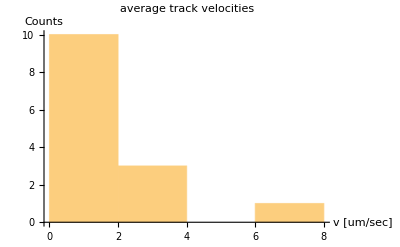
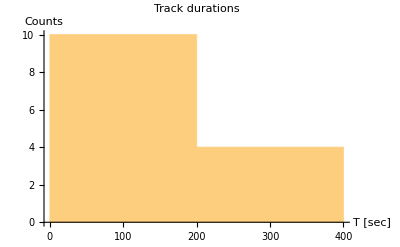
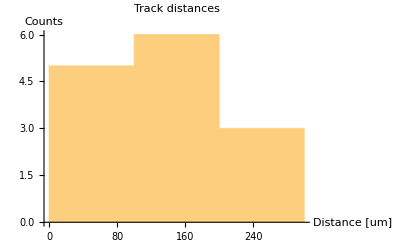
{{-Graphics-,-Graphics-,-Graphics-},{{pixelsize time= 1 sec,pixelsize space= 1 um},{Direction,Av frame2frame velocity [um/sec],track duration [sec],track total displacement [um],Start2end velocity [um/sec]},{1.,0.9229,248.,225.,0.9073},{1.,0.3389,299.,101.,0.3378},{-1.,0.3783,268.,101.,0.3769},{1.,1.1136,265.,294.,1.1094},{1.,3.2667,46.,147.,3.1957},{-1.,2.5645,63.,159.,2.5238},{0.,0.3415,42.,14.,0.3333},{1.,2.807,58.,160.,2.7586},{1.,0.3187,92.,29.,0.3152},{1.,7.973,38.,295.,7.7632},{1.,1.2778,19.,23.,1.2105},{-1.,0.3167,121.,38.,0.314},{-1.,1.871,63.,116.,1.8413},{1.,1.9,21.,38.,1.8095}}}

```mathematica
processed=pproc[results[[-1]] (*tracks are the last entry in the results*),1(*pixelsize time*),1(*pixelsize space*)]
```

```mathematica
(*Example table for further analysis*)
Dataset@processed[[-1,2;;]]
```